```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Github\collab-optimizer\data

```mathematica
GetCollabAvg[θ_,τ_]:=Module[{},
Mean[((Length[Cases[SplitBy[Get["microsim-theta_"<>θ<>"-tau_"<>τ<>"-run_"<>ToString[#]<>".txt"],Last[#]≥6&],{___,{_,6},___}]])/15)&/@Range[100]]
]
```

```mathematica
microdat=Table[{ToExpression@τ,GetCollabAvg[θ,τ]},{θ,{"0.1","1.0","10.0"}},{τ,{"3","4","5","6","7"}}]
```

{{{3,1198/125},{4,4753/500},{5,3518/375},{6,4613/500},{7,13579/1500}},{{3,10},{4,10},{5,4969/500},{6,3461/375},{7,1819/300}},{{3,10},{4,10},{5,10},{6,553/60},{7,1/15}}}

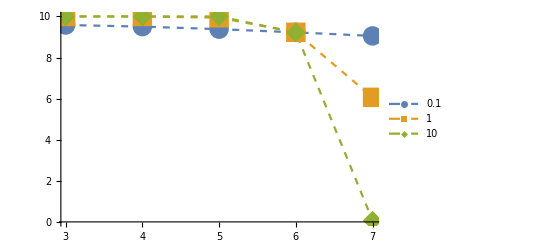

```mathematica
ListLinePlot[microdat,PlotStyle->Directive[Dashed,Thick],PlotMarkers->{Automatic,20},PlotLegends->{"0.1","1","10"},PlotRange->All]
```

```mathematica
microdat>>"AnalysedMicroDat.txt"
```

```mathematica
expdat=Get["task_alloc_0.txt"]
```

```mathematica
expdat//Dimensions
```

{15}

```mathematica
realdat=Partition[Riffle[{3,4,5,6,7},#],2]&/@Transpose@Partition[Mean[((Length[Cases[SplitBy[Select[#,First[#]≤ 15*60&],Last[#]≥ 4&],{___,{_,n_/;n≥ 4},___}]]&/@Get["task_alloc_"<>ToString[#]<>".txt"])&/@Range[0,4])/15],3]
```

{{{3,596/75},{4,587/75},{5,578/75},{6,622/75},{7,578/75}},{{3,529/75},{4,147/25},{5,353/75},{6,263/75},{7,196/75}},{{3,448/75},{4,114/25},{5,238/75},{6,163/75},{7,6/25}}}

```mathematica
realdat>>"AnalysedRealDat.txt"
```

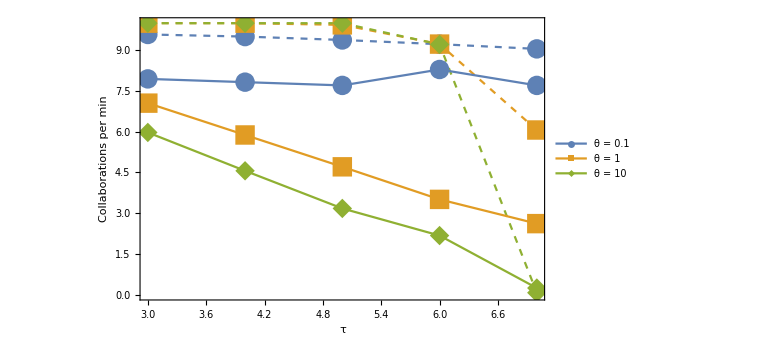

```mathematica
Show[ListLinePlot[microdat,PlotStyle->Directive[Dashed,Thick],PlotMarkers->{Automatic,20},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"τ","Collaborations per min"},ImageSize->Large,BaseStyle->FontSize->18],ListLinePlot[realdat,PlotStyle->Directive[Thick],PlotMarkers->{Automatic,20},PlotLegends->{"θ = 0.1","θ = 1","θ = 10"},PlotRange->All]]
```